# :d83d:dcab Bset 1: Orientation and Particle Motion

```mathematica
SetDirectory@NotebookDirectory[];
<<"../MMA library.m"
```

## Reflection

This document lives in Mathematica, so reflection and notes are formatted green instead of my normal blue.

## Euler Angle Review

```mathematica
With[{context="s1`"},If[Context[] ≠ context,Begin[context]]];Dynamic[Refresh[Context[],UpdateInterval->1]]
```

#### 1. What’s the Matrix?

```mathematica
yawMatrix=RotationMatrix[ψ,UnitVector[3,3]];
pitchMatrix=RotationMatrix[θ,UnitVector[3,2]];
rollMatrix=RotationMatrix[ϕ,UnitVector[3,1]];
```

```mathematica
rollMatrix.yawMatrix.pitchMatrix//MatrixForm
```

rollMatrix.yawMatrix.pitchMatrix

I’m not 100% solid about why this is “roll*pitch*yaw” instead of “pitch*yaw*roll”. Because the roll operation is applied last to the body, I want to multiply it first such that its effect isn’t affected by the other transformations (if that made any sense).

```mathematica
With[{context="s1`"},If[Context[]==context,End[]]];Dynamic[Refresh[Context[],UpdateInterval->1]]
```

## Build a Gimbal

```mathematica
With[{context="gimbal`"},If[Context[] ≠ context,Begin[context]]];Dynamic[Refresh[Context[],UpdateInterval->1]]
```

```mathematica
With[{context="gimbal`"},If[Context[]==context,End[],"Not in context"]]
```

## Gimbal Lock

### 8. What is gimbal lock?

Gimbal lock is a situation in which two points that are adjacent (or arbitrarily close) on a sphere have dramatically different representations as angles pointing to them. This usually (always?) occurs at singularities, like the poles of a pan-tilt-yaw coordinate system. When a system is in gimbal lock, moving a small amount in one direction requires coordinated and long motion of multiple axes, which can cause componentwise interpolation to fail. This is particularly challenging when dealing with a physical system in which the axes cannot reorient arbitrarily quickly or when dealing with an animation environment in which smooth interpolation is a critical feature of the system.

### 9. Find it.

In 3-1-3 Euler angles, gimbal lock occurs whenever the second rotation is 0. In this case, the first and third axes are collinear.

In 3-2-1 angles, gimbal lock occurs when the second rotation is ±90 degrees, because that again puts the first and third rings into parallel alignment.

## Particle Motion

I am a leaf on the wind. Watch how I soar.

```mathematica
With[{context="s4`"},If[Context[] ≠ context,Begin[context]]];Dynamic[Refresh[Context[],UpdateInterval->1]]
```

As a result of being in Mathematica, some of the rote transformation steps aren’t necessary for me to solve these types of problems (particularly converting second-order vector DE’s to first-order scalar DE’s). I know how to do them, but won’t be doing so unless actually necessary.

```mathematica
ClearAll[x,t,fg, fd,m,g,cd,d,ρ,w]
initialConditions={x[0]=={0,0,0},x'[0]==QuantityMagnitude@UnitConvert[Quantity[130, ("Miles")/("Hours")],Quantity[, ("Meters")/("Seconds")]]{0,1/Sqrt@2,1/Sqrt@2}}
(* Setup vector parameters *)
w={1,0,0};
(* Setup scalar parameters *)
params=<|m->0.05,g->9.8,cd->.25,d->4.27/100,ρ->1.29|>
(* define forces *)
fg[x_?(VectorQ[#]&)]:=m g{0,0,-1};fd[x_?(VectorQ[#]&)]:=-1/2 ρ cd (Pi d^2/4)(x'[t]-w)
simRange={t,0,10};

diffeqs={(fg[x[t]]+fd[x[t]]==m x''[t])}/.forces/.params;
Join[initialConditions,diffeqs] // TraditionalForm
events={WhenEvent[x[t][[3]]==0,
end=t;
distance=Norm[x[t]];
"StopIntegration"]};
```

{x[0]=={0,0,0},x'[0]=={0,(18161 √2)/625,(18161 √2)/625}}

<|m→0.05,g→9.8,cd→0.25,d→0.0427,ρ→1.29|>

{x(0)=={0,0,0},x'(0)=={0,(18161 √2)/625,(18161 √2)/625},{-0.000230911 (x'(t)-1),-0.000230911 x'(t),-0.000230911 x'(t)}(x(t))+{0,0,-0.49}(x(t))==0.05 x''(t)}

```mathematica
(fd)/.forces
```

{-0.000230911 (-1+x$35805'[t]),-0.000230911 x$35806'[t],-0.000230911 x$35807'[t]}

NDSolveValue::nbnum1: The function value x$42804[0.]==0 is not True or False when the arguments are {0.,0.,0.,0.,41.0937,0.,41.0937,0.,0.,41.0937,-0.18978,41.0937,-9.98978}.

NDSolveValue::nbnum1: The function value x$42804[4.32644×10^-6]==0 is not True or False when the arguments are {4.32644×10^-6,0.,0.,0.000177789,41.0937,0.000177789,41.0936,0.,0.,41.0937,-0.18978,41.0936,-9.98978}.

NDSolveValue::nbnum1: The function value x$42804[8.65289×10^-6]==0 is not True or False when the arguments are {8.65289×10^-6,0.,0.,0.000355579,41.0937,0.000355578,41.0936,0.,0.,41.0937,-0.18978,41.0936,-9.98978}.

General::stop: Further output of NDSolveValue::nbnum1 will be suppressed during this calculation.

{InterpolatingFunction[{{0., 10.}}, <>][t],InterpolatingFunction[{{0., 10.}}, <>][t],InterpolatingFunction[{{0., 10.}}, <>][t]}

335.929

-Graphics3D-

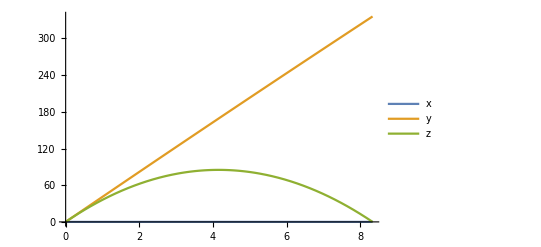

```mathematica
sol=NDSolveValue[Join[initialConditions,diffeqs,events],x[t],simRange]
distance
ParametricPlot3D[sol,{t,0,end},PlotLegends->{"projectile path"},AxesLabel->{"x","y","z"},PlotRange->Full]
Plot[{sol[[1]],sol[[2]],sol[[3]]},{t,0,end},PlotLegends->{"x","y","z"}]
```

```mathematica
With[{context="s4`"},If[Context[]==context,End[],"Not in context"]]
```

## Scratch Work

```mathematica
{1,2,3}-{1,3,5}
```

{0,-1,-2}

```mathematica
Unique[][t]
```

$82[t]

```mathematica
rhs[var_?(VectorQ[#] &)]:=var-{1,2};
rhs[{5,6}]
```

{4,4}

```mathematica
VectorQ@var
```

False